```mathematica
Quit[];
```

## Load and initialize HiggsTools

```mathematica
Install["/Path/To/HiggsTools/build/wstp/MHiggsTools"];\
HSInitialize["/Path/To/HSDataSet"];
```

------------------------------------------------------------------------------

HiggsTools 1.0

H. Bahl, P. Bechtle, T. Biekoetter, S. Heinmeyer, S. Paasch,

C. Li, G. Weiglein, J. Wittbrodt

------------------------------------------------------------------------------

## Add SM - like Higgs boson

```mathematica
HPAddParticle["H",125.09,"neutral","even"];

HPSMLikeEffCouplings["H"];
GammaTotSM=HPGetTotalWidth["H"];
```

## Evaluate Δχ^2

```mathematica
GetChisq[ceff_,branchingRatioNP_]:=Module[{totalWidthbefore,partialWidthNP},
HPScaledSMlikeEffCouplings["H",ceff];
totalWidthbefore=HPGetTotalWidth["H"];
partialWidthNP=branchingRatioNP totalWidthbefore/(1-branchingRatioNP);
HPSetDecayWidth["H","NP","NP",partialWidthNP];
HSGetChisq[]

]

calcDeltaChisq[list_]:=Module[{chisqmin,out},
chisqmin=Min[list[[;;,3]]];
out=list;
out[[;;,3]]-=chisqmin;
out
];
getMinChisq[list_]:=Module[{chisqmin,pos},
chisqmin=Min[list[[;;,3]]];
pos=Position[list[[;;,3]],chisqmin];
{list[[pos[[1,1]],1]],list[[pos[[1,1]],2]]}
];

GammaTot[ceff_,branchingRatioNP_]:=Module[{GammaTotNoBrNP},
GammaTotNoBrNP=ceff^2 GammaTotSM ;
GammaTotNoBrNP/(1-branchingRatioNP)
];
```

```mathematica
res=calcDeltaChisq[Flatten[Table[{ceff,brNP,GetChisq[ceff,brNP]},{ceff,0,5,.01},{brNP,0,.999,.01}],1]];
```

```mathematica
min=getMinChisq[res];
```

## Plotting

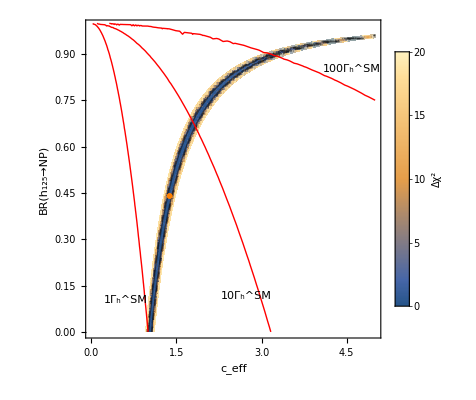

```mathematica
p1=ListDensityPlot[res,PlotLegends->BarLegend[Automatic,LegendLabel->"Δχ^2"],FrameLabel->{"c_eff","BR(h_125→NP)"},PlotRange->{0,20}];
p2=ListContourPlot[res,Contours->{2.3,4.61,6.18},ContourShading->None,ContourStyle->{Thick,{Thick,Dashed},{Thick,Dotted}}];
p3=ListPlot[{min},PlotMarkers->{Text[Style["✶",20]]},PlotStyle->{Orange}];
p4=ContourPlot[GammaTot[ceff,brNP]/GammaTotSM,{ceff,0,5},{brNP,0,.999},Contours->{1,10,100},ContourShading->None,ContourStyle->{{Red,Thick}},ContourLabels->(Text[Framed[ToString[#3]<>"Γ_h^SM"],{#1-.4,#2+0.1},Background->White]&)];
Show[p1,p2,p3,p4]
```